```mathematica
data2=Import["/Users/csul/github/workshop-python-hpc/benchmarkdata.txt","Data"]//Flatten;
```

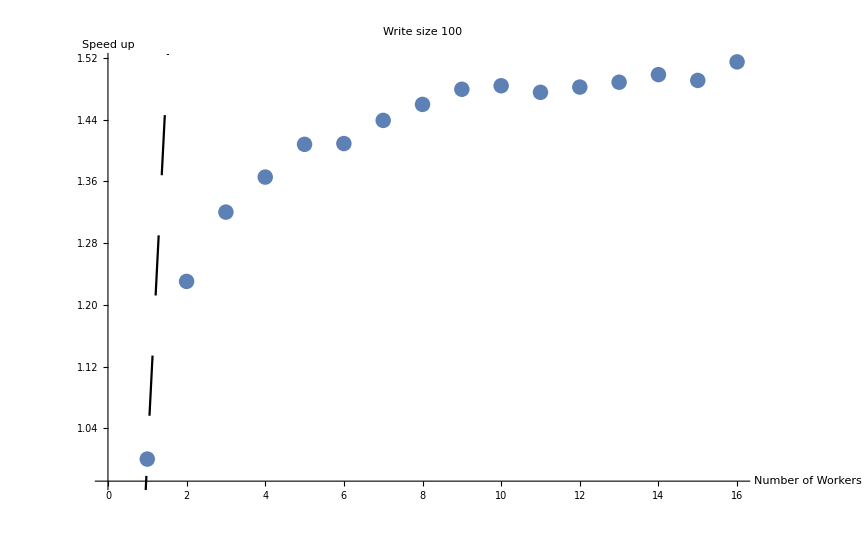

```mathematica
lp=ListPlot[{Max[data]/data},PlotLabel->"Write size 100",AxesLabel->{"Number of Workers","Speed up"},LabelStyle->Directive[FontSize->24]];
yx=Plot[x,{x,0,16},PlotStyle->{Dashing[0.05],Black}];
Show[lp,yx]
```

```mathematica
data[[1]]
```

4.009s

```mathematica
data2=Import["/Users/csul/github/workshop-python-hpc/benchmarkdata2.txt","Data"]//Flatten;
```

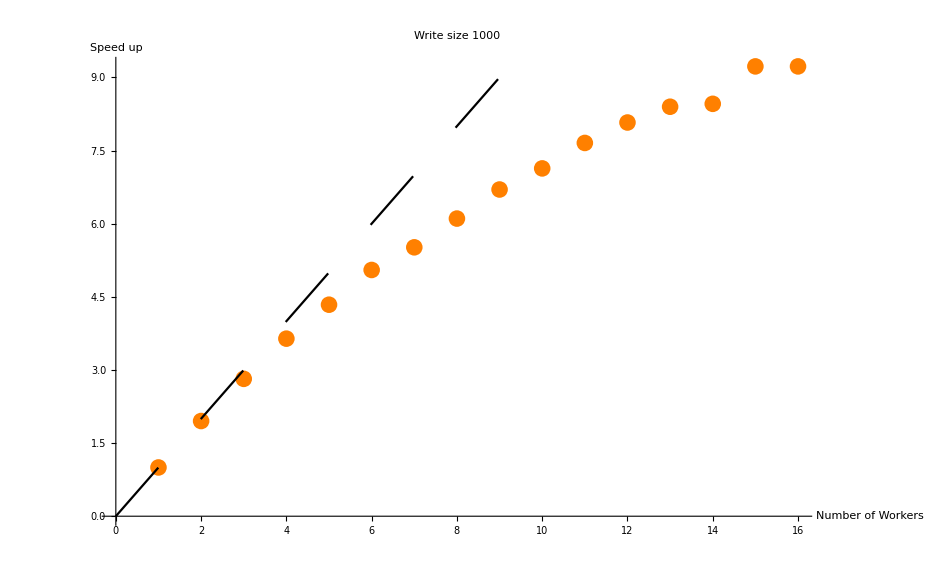

```mathematica
lp2=ListPlot[{Max[data2]/data2},PlotStyle->Orange,PlotLabel->"Write size 1000",AxesLabel->{"Number of Workers","Speed up"},LabelStyle->Directive[FontSize->24]];
Show[lp2,yx]
```

```mathematica
data3=Import["/Users/csul/github/workshop-python-hpc/benchmarkdata_mpi.txt","Data"]
y2=Max[data3]/data3[[All,2]];
x2=data3[[All,1]];
Thread[{x,y}]
```

{{1,133.742},{2,130.773},{3,86.683},{4,64.741},{5,52.071},{6,43.411},{8,32.942},{10,26.59},{12,23.316},{15,19.557},{16,17.954}}

{{1,1.},{2,1.0227},{3,1.54289},{4,2.0658},{5,2.56845},{6,3.08083},{8,4.05992},{10,5.02979},{12,5.73606},{15,6.83857},{16,7.44915}}

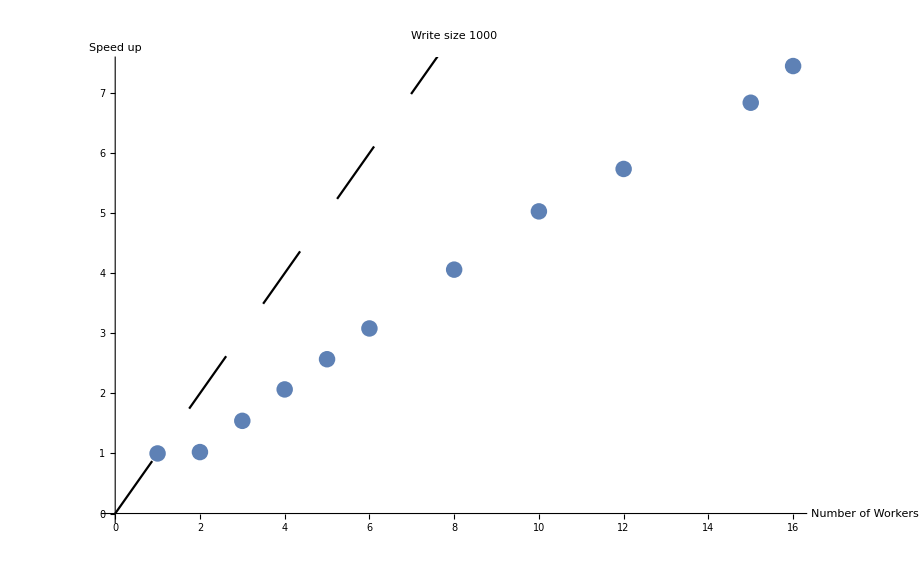

```mathematica
lp3=ListPlot[Thread[{x,y}],PlotLabel->"Write size 1000",AxesLabel->{"Number of Workers","Speed up"},LabelStyle->Directive[FontSize->24]];
Show[lp3,yx,PlotStyle->{Dashing[0.05],Black}]
```

{{1,140.415},{2,80.129},{3,54.609},{4,41.664},{5,34.72},{6,29.434},{8,22.885},{10,18.563},{12,14.4},{15,11.946},{16,11.228}}

{1,2,3,4,5,6,8,10,12,15,16}

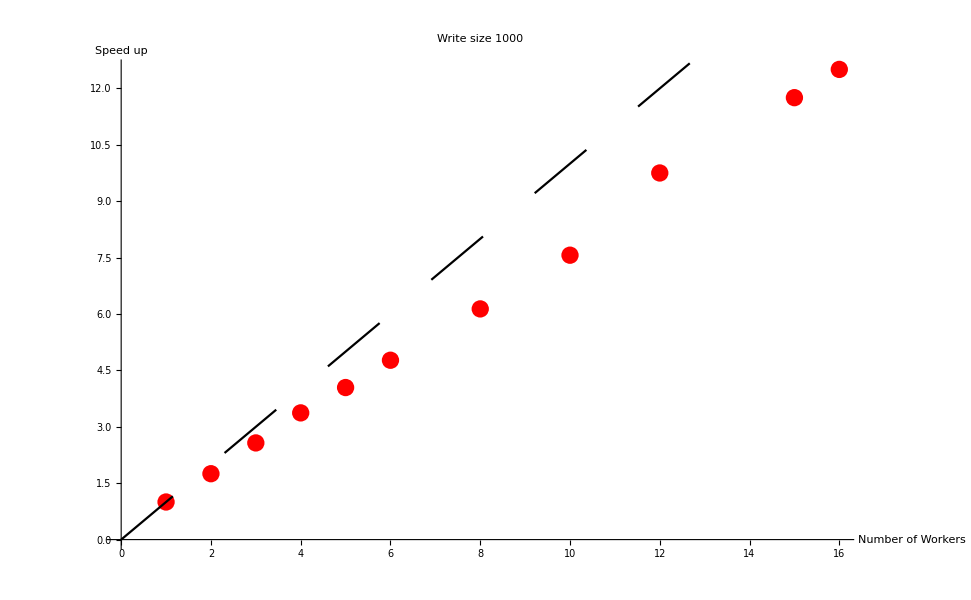

```mathematica
data4=Import["/Users/csul/github/workshop-python-hpc/benchmarkdata_mpisc.txt","Data"]
y4=Max[data4]/data4[[All,2]];
x4=data4[[All,1]]
lp4=ListPlot[Thread[{x4,y4}],PlotStyle->Red,PlotLabel->"Write size 1000",AxesLabel->{"Number of Workers","Speed up"},LabelStyle->Directive[FontSize->24]];
Show[lp4,yx,PlotStyle->{Dashing[0.05],Black}]
```